Вариант 4

Задание 1

Свободный член равен -40, поэтому один из корней будет лежать в пределах отрезка [-40; 40]

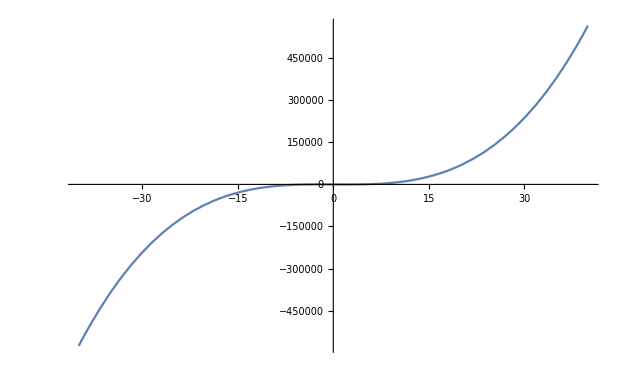

Судя по графику, решение лежит в пределах отрезка [-10; 10]

Найдём первый корень при помощи метода половинного деления, точность будет 10^-4

Найден корень x = 4.00002 получено на 18 шаге.

Очевидно, что корнем будет не 4.0002, а просто 4

Поделив исходный многочлен на многочлен (x-4), получим

Найдём корни квадратного уравнения при помощи дискриминанта

x1 = -10/3; x2 = -1/3;

Ответ: -10/3, -1/3, 4;

```mathematica
"Вариант 4"

"Задание 1"

f[x_] := 9x^3-3x^2-122x-40;
"Свободный член равен -40, поэтому один из корней будет лежать в пределах отрезка [-40; 40]"
Plot[{f[x]}, {x, -40, 40}]
"Судя по графику, решение лежит в пределах отрезка [-10; 10]"
"Найдём первый корень при помощи метода половинного деления, точность будет 10^-4"
e = 10^-4; a = -10; b = 10;
Do[c = (a+b)/2.;
fc = f[c];
If[f[a]*fc<0,b=c, If[fc!=0,a=c]];
If[Abs[b-a]<e||fc==0,
Print["Найден корень x = ",  c //N, " получено на ", n,  " шаге."];
Break[]],
{n, 1, 100}
]
"Очевидно, что корнем будет не 4.0002, а просто 4"
"Поделив исходный многочлен на многочлен (x-4), получим"
g[x_] := 9x^2+33x+10;
"Найдём корни квадратного уравнения при помощи дискриминанта"
a = 9; b = 33; c = 10;
disc = b^2-4*a*c;
x1 = (-b - Sqrt[disc])/(2*a); x2 = (-b + Sqrt[disc])/(2*a);
Print["x1 = ", x1, "; x2 = ", x2, ";"]
Print["Ответ: ", x1, ", ", x2, ", 4;"]
```